#### Úlohy na samostatnú prácu

Vypočitajte nasledovné príklady. Dajte pozor na prioritu operácií!.

2+3/5=

```mathematica
2+3/5
```

13/5

(2+3)/5=

```mathematica
(2+3)/5
```

1

(2+3)/(7+8)=

```mathematica
(2+3)/(7+8)
```

1/3

2 . 3/5=

```mathematica
2 3/5
```

6/5

2.3/5=

```mathematica
(2 3)/5
```

6/5

2/3.5=

```mathematica
2/(3 5)
```

2/15

8^(2/3)=

```mathematica
8^(2/3)
```

4

8^2/3=

```mathematica
8^2/3
```

64/3

√8281=

```mathematica
Sqrt[8281]
```

91

(√8264)/16=

```mathematica
Sqrt[8281]/16
```

91/16

√(8264/(0,16))=

```mathematica
Sqrt[8281]/0.16
```

568.75

#### Úlohy na samostatnú prácu

Vypočítajte funkčné hodnoty nasledovných funkcií
	a) presne
	b) približne

sin(4)

```mathematica
Sin[4]
```

Sin[4]

```mathematica
Precision[Sin[4]]
Sin[4]
```

∞

Sin[4]

sin(4 °)

```mathematica
Sin[4Degree]
Precision[Sin[4Degree]]
```

Sin[4 °]

∞

cos (35,2)

```mathematica
Cos[35.2]
```

-0.800612

```mathematica
Precision[Cos[35.2]]
Cos[35.2]
```

MachinePrecision

-0.800612

sin π

```mathematica
Sin[Pi]
```

0

cos 90°

```mathematica
Cos[90 Degree]
```

0

tg π/4

```mathematica
Tan[Pi/4]
```

1

cotg 45°

```mathematica
Cot[45 Degree]
```

1

arcsin 1

```mathematica
ArcSin[1]
```

π/2

arctg 1

```mathematica
ArcTan[1]
```

π/4

ln 100

```mathematica
Log[E, 100]//N
Precision[Log[E, 100]]
```

4.60517

∞

ln E

```mathematica
Log[E,E]
```

1

log 100

```mathematica
Log[100]
```

Log[100]

log_10100

```mathematica
Log[10,100]
```

2

log_10010

```mathematica
Log[100,10]
```

1/2

|-3|

```mathematica
Abs[-3]
```

3

ln (-5)

```mathematica
Log[E, -5]
```

ⅈ π+Log[5]

#### Úlohy na samostatnú prácu

Daný je výraz ((x^2-5x+6)^2)/(((x-3)^5)^(1/3)).((x+3)^(1/3)/(x-2)^2). 

a) Výraz zjednodušte a vypočítajte jeho hodnotu pre x = 5.
b) Potom ku výrazu pripočítajte (x+1) a celý výraz umocnite na druhú. 
c) Vypočítajte hodnotu výsledného výrazu pre x=-3.2

```mathematica
(*a*)
Simplify[((x^2 - 5*x + 6)^2)/CubeRoot[(x-3)^5] * (CubeRoot[x+3]/(x-2)^2)]
```

```mathematica
((-3+x)^2 (3+x)^(1/3))/(((-3+x)^5)^(1/3))
x = 5;
x
Clear[x];
(*b*)
(((-3+x)^2 (3+x)^(1/3))/(((-3+x)^5)^(1/3)) + (x+1))^2
```

((-3+x)^2 (3+x)^(1/3))/(((-3+x)^5)^(1/3))

5

(1+x+((-3+x)^2 (3+x)^(1/3))/(((-3+x)^5)^(1/3)))^2

```mathematica
(1+x+((-3+x)^2 (3+x)^(1/3))/(((-3+x)^5)^(1/3)))^2
(*c*)
x=-3.2;
(1+x+((-3+x)^2 (3+x)^(1/3))/(((-3+x)^5)^(1/3)))^2
```

1.26712

1.26712

#### Úlohy na samostatnú prácu

Daný je výraz ((a+b)/(a-b)-(a-b)/(a+b)):(1-(a^2+b^2)/(a^2-b^2)). 

a) Výraz zjednodušte a vypočítajte jeho hodnotu pre  a = -3.4
b) Výraz zjednodušte a vypočítajte jeho hodnotu pre a = 3.2, b = 1.5

```mathematica
(**)
Clear[a]
Simplify[((a+b)/(a-b)-(a-b)/(a+b))/(1-(a^2+b^2)/(a^2-b^2))]
```

-(2 a)/b

```mathematica
-(2 a)/b
a=-3.2;
```

6.4/b

```mathematica
(*b*)
Clear[a,b];
Simplify[((a+b)/(a-b)-(a-b)/(a+b))/(1-(a^2+b^2)/(a^2-b^2))]
a = 3.2;
b=1.5;
-(2 a)/b
```

-(2 a)/b

-4.26667

#### Úlohy na samostatnú prácu

Nakreslite grafy funkcí na intervale [-2 π, 2 π] .

a)	 sin x

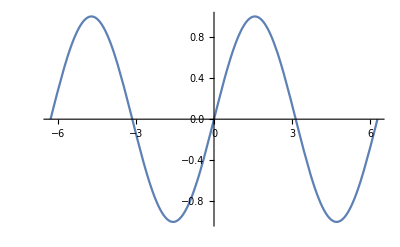

```mathematica
Plot[Sin[x],{x,-2*Pi,2*Pi}]
```

b)	 sin^2 x

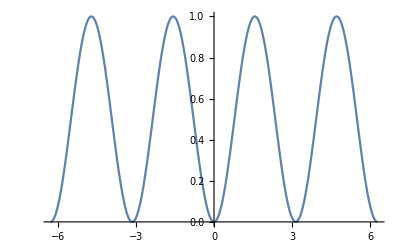

```mathematica
Plot[Sin[x]^2,{x,-2*Pi,2*Pi}]
```

c)	 sin (x^2)

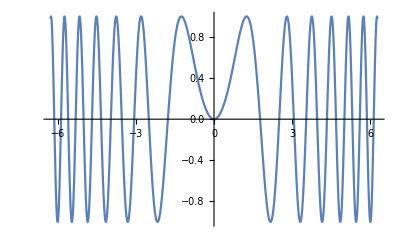

```mathematica
Plot[Sin[x^2],{x,-2*Pi,2*Pi}]
```

d)	 (sin x)^2

```mathematica
Plot[Sin[x]^2,{x,-2*Pi,2*Pi}]
```

-Graphics-

e)	2 sin (x/2)^2

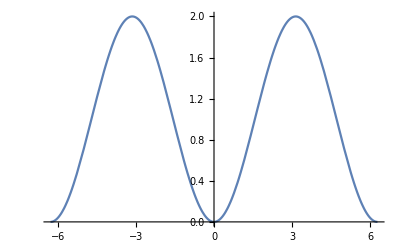

```mathematica
Plot[2 Sin[x/2]^2,{x,-2*Pi,2*Pi}]
```

#### Úlohy na samostatnú prácu

Nakreslite grafy funkcí na intervale [-2 π, 2 π] .

a)	 cos x

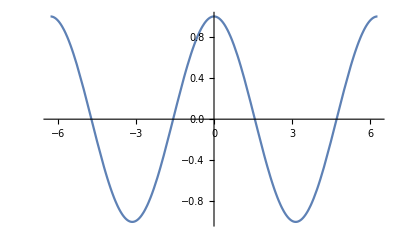

```mathematica
Plot[Cos[x],{x,-2*Pi,2*Pi}]
```

b)	 2 cos x

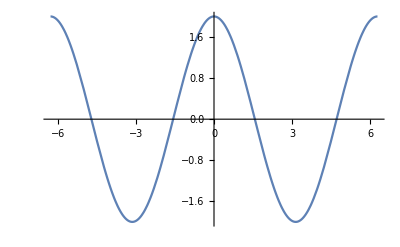

```mathematica
Plot[2 Cos[x],{x,-2*Pi,2*Pi}]
```

c)	 cos (2x)

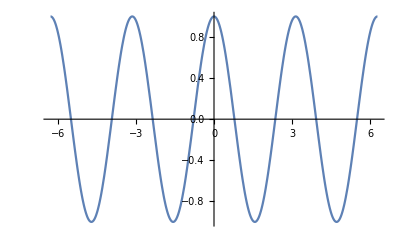

```mathematica
Plot[Cos[2 x],{x,-2*Pi,2*Pi}]
```

d)	 cos x/2

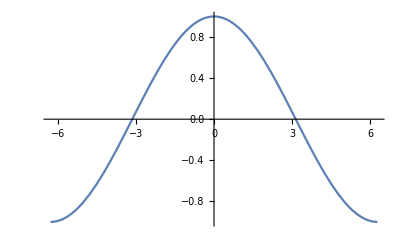

```mathematica
Plot[Cos[x/2],{x,-2*Pi,2*Pi}]
```

e)	2 cos(x^2)

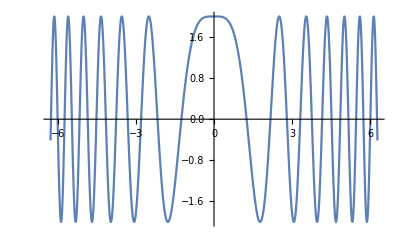

```mathematica
Plot[2 Cos[x^2],{x,-2*Pi,2*Pi}]
```

#### Úlohy na samostatnú prácu

Nakreslite grafy funkcí na  vhodnom intervale.

a) 	ln x

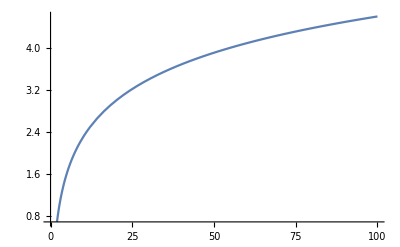

```mathematica
Plot[Log[E, x],{x,0,100}]
```

b)	log x

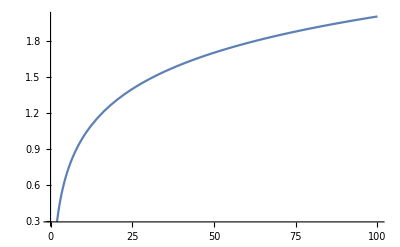

```mathematica
Plot[Log[10, x],{x,0,100}]
```

c)	log_2 x

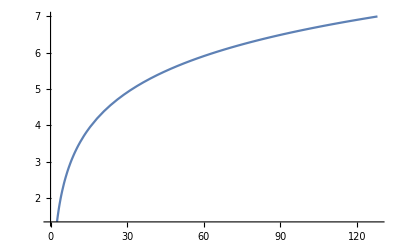

```mathematica
Plot[Log[2, x],{x,0,128}]
```

d)	e^x

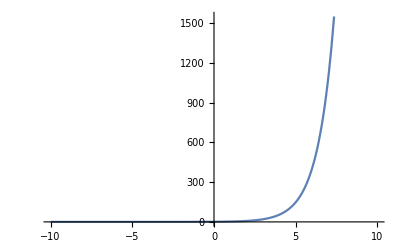

```mathematica
Plot[Exp[x],{x,-10,10}]
```

e) 	e^-x

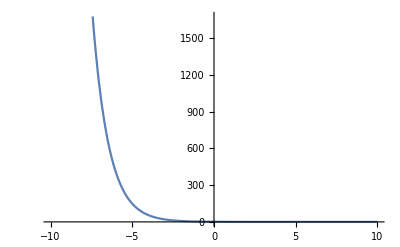

```mathematica
Plot[Exp[-x],{x,-10,10}]
```

f)	1/e^(x+4)

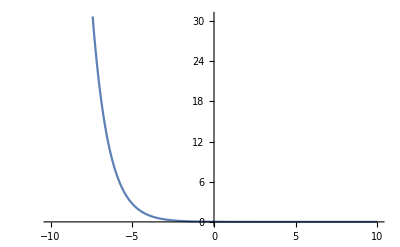

```mathematica
Plot[1/Exp[x+4],{x,-10,10}]
```

g) 	|x-2|

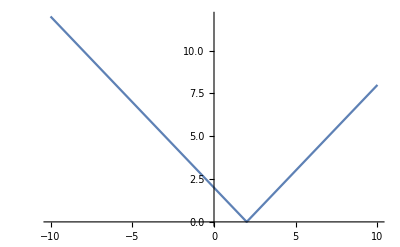

```mathematica
Plot[Abs[x-2],{x,-10,10}]
```

#### Úlohy na samostatnú prácu

Nakreslite graf funkcie sin^2 x-√3 sin x+(x-4)/(x^2-x+3) na  vhodnom intervale a vypočítajte hodnotu funkcie v bodoch x=1, 2.3, 4.6 .

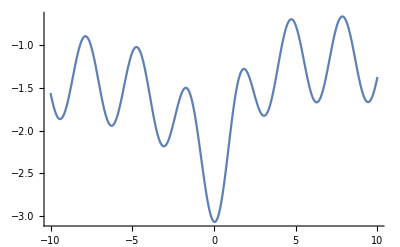

-1-√3+Sin[1]^2

-1.45978

-0.713954

```mathematica
equation = Sin[x]^2 - Sqrt[3]+(x-4)/(x^2-x+3);
Plot[equation,{x,-10,10}]
x = 1;
equation
Clear[x];
x = 2.3;
equation
Clear[x];
x = 4.6;
equation
Clear[x];
```

#### Úlohy na samostatnú prácu

Do premennej a  zapíšte hodnotu výrazu (x+y)^2/x^2+(x^2-y^2)/(x+3y-x^3)-5/7 pre x=5.2 a y=-2.5.
Do premennej b  zapíšte hodnotu výrazu (x+y)^3/(x^2+3)+x/y pre x=5 a y=-6.2.
Potom premenné a a b sčítajte.

```mathematica
a = (x+y)^2/x^2+ (x^2 - y^2)/(x+3 y - x^3)-5/7;
x = 5.2;
y = -2.5;
a
Clear[x,y];
b = (x + y)^3/(x^2 + 3)+ x/y;
x = 5;
y = -6.2;
b
a+b
```

-0.590163

-0.868166

-1.42788

#### Úlohy na samostatnú prácu

Definujte funkciu f: y=√((5x-1)/(x^2+1))

```mathematica
Clear[y,x];
y[x_]= Sqrt[(5x - 1)/(x^2 +1)];
y[1]
```

√2

a) Nakreslite graf danej funkcie na vhodnom intervale.

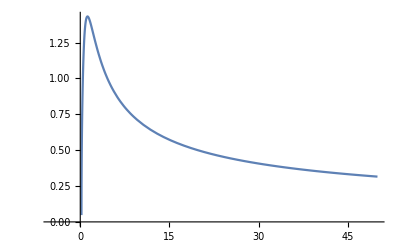

```mathematica
Plot[y[x],{x, -5, 50}]
```

b) Vypočítajte hodnotu funkcie v bode x = 1.

```mathematica
y[1]
```

√2

c) Vyčistite pamäťové miesto.

```mathematica
Clear[y]
```

#### Úlohy na samostatnú prácu

Definujte funkciu f: y=ln(√((5x-1)/(x^2+1)))

```mathematica
y[x_] = Log[E,Sqrt[(5x - 1)/(x^2 + 1)]];
```

a) Nakreslite graf danej funkcie na vhodnom intervale.

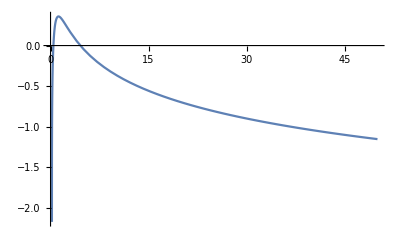

```mathematica
Plot[y[x],{x, 0, 50}]
```

b) Vypočítajte hodnotu funkcie v bode x =1/5.

```mathematica
y[1/5]
```

-∞

c) Vyčistite pamäťové miesto.

```mathematica
Clear[y]
```

#### Úlohy na samostatnú prácu

Obsah kruhu je možné vypočítať podľa vzťahu S=π . r^2.

a) Definujte funkciu S  na výpočet obsahu kruhu podľa predchádzajúceho vzťahu.

```mathematica
s[r_]=Pi r^2;
```

b) Vypočítajte s použitím tejto funkcie obsah kruhu s polomerom r=2.53 cm.  
	Výsledok: 20.109 [cm^2]

```mathematica
s[2.53]
```

20.109

#### Úlohy na samostatnú prácu

Obvod kruhu je možné vypočítať podľa vzťahu o=2.π . r. 
	a) Definujte funkciu o  na výpočet obvodu kruhu podľa predchádzajúceho vzťahu.
	b) Vypočítajte s použitím tejto funkcie obsah kruhu s polomerom d=84.2 cm. 
	Výsledok: 264.522 [cm]

#### Úlohy na samostatnú prácu

Dráha rovnomerného pohybu s [km] v závislosti od rýchlosti v [km/h] pri danom čase t [h] sa vypočíta podľa vzťahu s=v.t
	a) Definujte funkciu s na výpočet dráhy ako funkciu dvoch premenných.
	b) Vypočítajte akú dráhu predje automobil idúci rovnomenou rýchlosťou 110 km/h za čas 6 min.
      	Výsledok: 11 [km]

#### Úlohy na samostatnú prácu

Dráha rovnomerného pohybu s [m] pri voľnom páde telesa v závislosti od času t [s] sa vypočíta podľa vzťahu s=1/2 g t^2
	a) Definujte konštantu g .
	b) Definujte funkciu s na výpočet dráhy ako funkciu času.
	c) Vypočítajte akú dráhu prejde teleso padajúce voľným pádom  z výšky 2 km za čas 20 s. 
	Stihne dopadnúť na zem za tento čas?

#### Úlohy na samostatné počítanie

Nájdite riešenie nasledujúcich rovníc. Stanovte aj podmienky riešiteľnosti.

a)	1/2(3x−1/2)−1/3(4x−1/3)=1/4(6x−5)−2/3.

```mathematica
Solve[1/2(3x - 1/2)-1/3 (4x - 1/3) == 1/4(6x - 5) - 2/3,x]
```

{{x→4/3}}

b)	√(x √x-x)+√x=x		x ∈ ℝ

```mathematica
Solve[Sqrt[x Sqrt[x]-x]+Sqrt[x]==x,x,Reals]
```

{{x→0},{x→1},{x→4}}

c)	3 (4^x+9^(x+1))=2 . (3 . 4^(x+1)-1/4 . 9 . 9^x)

```mathematica
Solve[3(4^x+9^(x+1))==2(3 4^(x+1)-1/4 9 9^x),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(2 Log[3]-Log[6])/(2 (Log[2]-Log[3]))}}

d)	√((7-x)/(3+x))+3 . √((3+x)/(7-x))=4

```mathematica
Solve[Sqrt[(7-x)/(3+x)]+3 Sqrt[(3 +x)/(7-x)]==4,x]
```

{{x→-2},{x→2}}

e)	2^(4 sin^2 x)+2^(2(1+cos 2x))-10=0

```mathematica
Solve[2^(4 Sin[x]^2)+ 2^(1+Cos[2 x])-10 ==0, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-10+2^(1+Cos[2 x])+2^(4 Sin[x]^2)==0,x]

#### Úlohy na samostatné počítanie

Nájdite všetky reálne riešenia nasledujúcich rovníc. Stanovte aj podmienky riešiteľnosti.

a)	x^5+4 x^4−5 x^3+2 x^2−2x=0.

```mathematica
Solve[x^5 + 4 x^4 - 5 x^3 + 2 x^2 - 2 x ==0, x, Reals]
```

{{x→0},{x→1},{x→Root-5.08Root[2+5 #1^2+#1^3&,1]-5.077574223045071}}

b)	2^x . (1/8)^(1-x)+ 2^(1-x) . (1/8)^x=1

c)	e^(−x^2)=2 x^2−3x.

d)	ln(x+3)=sin3x

e)	log x^(2 . log √x)+log(1/x^2)=3

#### Úlohy na samostatné počítanie

Nájdite všetky riešenia nasledujúcich rovníc. Stanovte aj podmienky riešiteľnosti.

a)	3 . 2^(log x)+8 . 2^(-log x)=5(1+10 log 100^(1/5))
	b)	1/2(4x−2)+2/3(2−3x)=−2.
	c)	1+x √(x+7/4)=1-x			x ∈ ℝ
	d)	√(2 x - 9 +√(3x-5))-√(2x-9-√(3x-5))=2		x ∈ ℝ
	e)	x^(log^2 x^2-3log x - 9/2)=10^(-2log x)

#### Úlohy na samostatné počítanie

Nájdite všetky riešenia nasledujúcich rovníc. Stanovte aj podmienky riešiteľnosti.

a)	(x−1)/4−(x−2)/6=(x+1)/12
	b)	−(x+1)+2 √(x^2+1)−3(x^3+1)^(1/3)+5(x^5+1)^(1/5)−4=0.
	c)	x^x-x^-x=3(1+x^-x)		x ∈ ℤ-{0}
	d)	√(3^(4x)+1)+√(2 . 3^(4x)+3)=5
	e)	81^x-9^(x+1)=3 . log_3(1/27)+3^(2x)

#### Úlohy na samostatné počítanie

Nájdite všetky riešenia nasledujúcich rovníc. Stanovte aj podmienky riešiteľnosti.
	a)	log(x^3+1)-log 7-log x=log(x+1)-log 6
	b)	x−cos x−1/4=0 z intervalu [-2,2]
	c)	√(1+x √(x^2+4))=1-x		x ∈ ℤ
	d)	log_5 x+3^(log_3 x)=7
	e)	√(x+3-4 √(1-x))=1+√x	x ∈ ℝ

#### Úlohy na samostatné počítanie

Nájdite riešenie sústavy rovníc 
a)  x + y + z = 3 , x - 2 y + 3 z = 1 , 2 x - y - z = 0

```mathematica
Solve[{x+y+y==3, x-2y + 3z ==1, 2x - y -z ==0}, {x,y,z}]
```

{{x→17/19,y→20/19,z→14/19}}

b)  x + y + z = 3 , x - 2 y + 3 z = 1 , 2 x - y + 4 z = 4

c)  x + y + z = 3 , x - 2 y + 3 z = 1 , 2 x - y + 4 z = 5

#### Úlohy na samostatné počítanie

Nájdite riešenie sústavy rovníc a správne interpretujte získaný výsledok.
	a)	2x | + | y | − | 3z | = | 10
3x | + | 2y | + | 3z | = | 2
x | + | 6y | − | 5z | = | 6
	
	b)	2x | + | y | − | 3z | = | 10
3x | + | 2y | + | 3z | = | 2
x | + | y | + | 6z | = | −8
	
	c)	2x | + | y | − | 3z | = | 10
3x | + | 2y | + | 3z | = | 2
x | + | y | + | 6z | = | 8.

#### Úlohy na samostatnú prácu

Zadefinujte funkciu f: y = ln^2 x+√(x+2)

```mathematica
y[x_]=Log[E,x]^2 + Sqrt[x+2]
```

√(2+x)+Log[x]^2

a)   Vypočítajte hodnotu funkcie v bode x=6.

```mathematica
y[6]
```

2 √2+Log[6]^2

b)   Zobrazte graf f(x) na intervale x∈[-5,5]. Aký je definičný obor tejto funkcie?

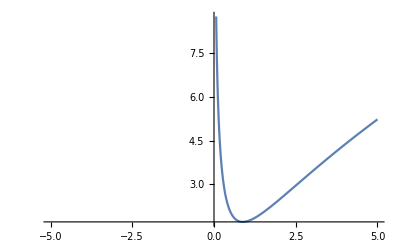

```mathematica
Plot[y[x],{x,-5,5}]
```

c)   Zobrazte graf f(x) na intervale x ∈ [-5, 5] a na celom jej obore hodnôt H(f).

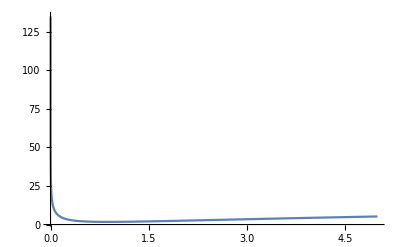

```mathematica
Plot[y[x],{x,-5,5}, PlotRange->All]
```

d)   Zobrazte graf f(x) na intervale x ∈ [-5, 5] a pre hodnoty y∈[0,5].

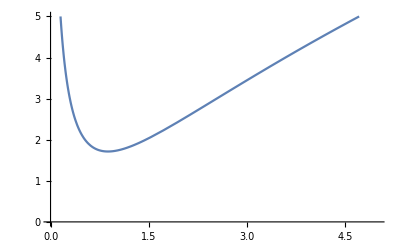

```mathematica
Plot[y[x],{x,-5,5}, PlotRange->{0,5}]
```

e)  Na grafe f(x) označte a pomenujte súradnicové osi x⃗  a y⃗.

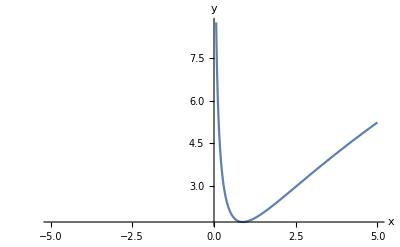

```mathematica
Plot[y[x],{x,-5,5}, AxesLabel->{"x", "y"}]
```

f)   Zobrazte graf  f(x) tenkou čiarou (Thick).

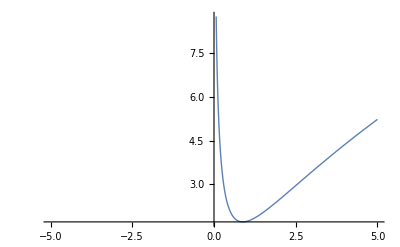

```mathematica
Plot[y[x],{x,-5,5}, PlotStyle->Thick]
```

g)   Zobrazte graf  f(x) čiarkovanou čiarou.

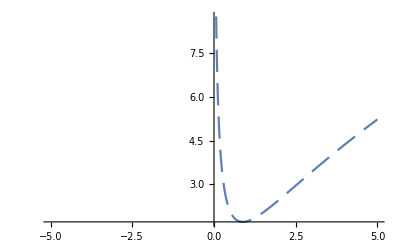

```mathematica
Plot[y[x],{x,-5,5}, PlotStyle->Dashing[{0.04,0.02}]]
```

h)   Zobrazte graf  f(x) zelenou čiarou  (Green)

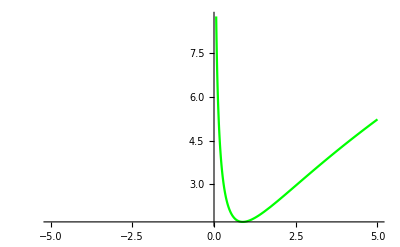

```mathematica
Plot[y[x],{x,-5,5}, PlotStyle->Green]
```

#### Úlohy na samostatnú prácu

Zadefinujte funkciu f: y = sin x^2+(x-4)^(1/3)
	a)   Vypočítajte hodnotu funkcie v bode x=6.
	b)   Zobrazte graf f(x) na intervale x∈[-5,5]. Aký je definičný obor tejto funkcie?
	c)   Zobrazte graf f(x) na intervale x ∈ [-5, 5] a na celom jej obore hodnôt H(f).
	d)   Zobrazte graf f(x) na intervale x ∈ [-5, 5] a pre hodnoty y∈[0, 10].
	e)  Na grafe f(x) označte a pomenujte súradnicové osi x⃗  a y⃗.
	f)   Zobrazte graf  f(x) hrubou čiarou (Thick).
	g)   Zobrazte graf  f(x) čiarkovanou čiarou.
	h)   Zobrazte graf  f(x) oranžovou čiarou  (Orange)

#### Úlohy na samostatnú prácu

Zadefinujte funkciu f: y = cos^2 x+(x+2)^(1/3)
	a)   Vypočítajte hodnotu funkcie v bode x=6.
	b)   Zobrazte graf f(x) na intervale x∈[-5,5]. Aký je definičný obor tejto funkcie?
	c)   Zobrazte graf f(x) na intervale x ∈ [-5, 5] a na celom jej obore hodnôt H(f).
	d)   Zobrazte graf f(x) na intervale x ∈ [-5, 5] a pre hodnoty y∈[0, 10].
	e)  Na grafe f(x) označte a pomenujte súradnicové osi x⃗  a y⃗.
	f)   Zobrazte graf  f(x) tenkou čiarou (Thick).
	g)   Zobrazte graf  f(x) čiarkovanou čiarou.
	h)   Zobrazte graf  f(x) zelenou čiarou  (Green)

#### Úlohy na samostatnú prácu

Je daná f: y =1-x +ln(x)  a g: y = 2 √(4-x^2)

a)     Zobrazte grafy f(x) a g(x) na definičnom obore funkcie g(x), v mierke x : y = 1 : 1  (Option: AspectRatio→1), pričom graf f(x) bude bude modrý, graf g(x) bude čiarkovaný, červený a hrubšou čiarou.

b)   Pomenujte na grafe (v jednom obr.) súradnicové osi.

c)   Vypočítajte f(5) a hodnotu funkcie g(1.2)

d)   Nájdite priesečník grafov, ak existuje.

#### Úlohy na samostatnú prácu

Je daná f: y =1+x^2 +log (x)  a g: y = √(x^2-7)
	a)     Zobrazte grafy f(x) a g(x) na definičnom obore funkcie g(x), v mierke x : y = 1 : 1  (Option: AspectRatio→1), pričom graf f(x) bude bude zelený, čiarkovaný, graf g(x) bude oranžový a hrubšou čiarou. 
	 b)   Pomenujte na grafe (v jednom obr.) súradnicové osi.
	 c)   Vypočítajte f(5) a hodnotu funkcie g(5.2)
	 d)   Nájdite priesečník grafov, ak existuje.

#### Úlohy na samostatnú prácu

Je daná f: y =1+√x +sin (x)  a g: y = tg (x^2-7)
	a)     Zobrazte grafy f(x) a g(x) na definičnom obore funkcie g(x), v mierke x : y = 1 : 1  (Option: AspectRatio→1), pričom graf f(x) bude bude svetlomodrý, čiarkovaný, graf g(x) bude zelený a hrubšou čiarou. 
	 b)   Pomenujte na grafe (v jednom obr.) súradnicové osi.
	 c)   Vypočítajte f(5) a hodnotu funkcie g(3.2)
	 d)   Nájdite priesečník grafov, ak existuje.

#### Úlohy na samostatnú prácu

Obsah kruhu je možné vypočítať podľa vzťahu S=π . r^2. 
	a) Definujte funkciu S  na výpočet obsahu kruhu podľa predchádzajúceho vzťahu.
	b) Vypočítajte s použitím tejto funkcie obsah kruhu s polomerom r=2.53 cm.  
	Výsledok: 20.109 [cm^2]

#### Úlohy na samostatnú prácu

Objem gule je možné vypočítať podľa vzťahu V=4/3 π . r^3. 
	a) Definujte funkciu  V  na výpočet objemu gule podľa predchádzajúceho vzťahu.
	b) Vypočítajte s použitím tejto funkcie objem gule s polomerom r=1.56 cm.  
	Výsledok: 15.9024  [cm^3]

#### Úlohy na samostatnú prácu

Obvod kruhu je možné vypočítať podľa vzťahu o=2.π . r. 
	a) Definujte funkciu o  na výpočet obvodu kruhu podľa predchádzajúceho vzťahu.
	b) Vypočítajte s použitím tejto funkcie obvodu kruhu s polomerom r=84.2 cm. 
	Výsledok: 264.522 [cm]

#### Úlohy na samostatnú prácu

Povrch gule je možné vypočítať podľa vzťahu P=4π . r^2. 
	a) Definujte funkciu  P  na výpočet povrchu gule podľa predchádzajúceho vzťahu.
	b) Vypočítajte s použitím tejto funkcie povrch gule s polomerom r=1.56 cm.  
	Výsledok: 30.5815  [cm^2]

#### Úlohy na samostatnú prácu

Dráha rovnomerného pohybu s [km] v závislosti od rýchlosti v [km/h] pri danom čase t [h] sa vypočíta podľa vzťahu s=v.t
	a) Definujte funkciu s na výpočet dráhy ako funkciu dvoch premenných.
	b) Vypočítajte akú dráhu prejde automobil idúci rovnomenou rýchlosťou 110 km/h za čas 6 min  (pozor na konverziu, počítať musíme v sekundách)
      	Výsledok: 11 [km]

#### Úlohy na samostatnú prácu

Obsah trojuholníka je možné vypočítať podľa vzťahu  S=(a.v_a)/2. 
	a) Definujte funkciu S ako funkciu dvoch premenných (základňa a výška) na výpočet obsahu trojuholníka podľa predchádzajúceho vzťahu.
	b) Vypočítajte s použitím tejto funkcie obsah trojuholníka so základňou a=5 cm a výškou v_a=6.2 cm 
	Výsledok: 15.5 [cm^2]

#### Úlohy na samostatnú prácu

Dráha rovnomerného pohybu s [m] pri voľnom páde telesa v závislosti od času t [s] sa vypočíta podľa vzťahu s=1/2 g t^2
	a) Definujte konštantu g .
	b) Definujte funkciu s na výpočet dráhy ako funkciu času.
	c) Vypočítajte akú dráhu prejde teleso padajúce voľným pádom  z výšky 2 km za čas 20 s. 
	Stihne dopadnúť na zem za tento čas?

#### Úlohy na samostatnú prácu

Rýchlosť rovnomerného pohybu v [m/s] pri voľnom páde telesa v závislosti od času t [s] sa vypočíta podľa vzťahu v=g t
	a) Definujte konštantu g .
	b) Definujte funkciu v na výpočet rýchlosti ako funkciu času.
	c) Vypočítajte akú rýchlosť dosiahne teleso padajúce voľným pádom  z výšky 2 km za čas 4.5 s.

#### Úlohy na samostatnú prácu

Motorové vozidlo ide po suchej asfaltovej ceste rýchlosťou v = 60 km/h.Vodič zbadá prekážku. Reakčná doba je jedna sekunda, potom nasleduje brzdenie. Vytvorte funkciu na výpočet dráhy s  [m], ktorú vozidlo prejde za čas t  [s] od okamihu zbadania prekážky. Nakreslite graf funkcie na intervale t∈[ 0, 10] sekúnd. Vytvorte tabuľku závislosti prejdenej dráhy od času t pre  t∈[ 0, 10] sekúnd. Nakreslite graf funkcie danej tabuľkou. Obidva grafy zobrazte v jednom obrázku.

Návod:
Dráhu s  [m] počítame ako hodnotu funkcie: s=v t  pre t z intervalu < 0 s, 1 s > (reakčná doba) a s=v t -1/2 μ g (t-1)^2 ,    pre t > 1 s  (brzdenie), kde   μ = 0,8   je súčiniteľ priľnavosti pre suchý asfalt, g = 9,81 ms-2  je gravitačné zrýchlenie, v [ ms-1]  je počiatočná rýchlosť vozidla.

#### Úlohy na samostatnú prácu

Definujte funkciu f (x), ak je daná predpisom
		f(x)={ tg(x)           x≥π;  
-x^2         x<π
a) Správnosť definície overte výpočtom pre x z oboch intervalov.
b) Graf funkcie f (x) nakreslite modrou, hrubou a čiarkovanou čiarou a vyznačte súradnicové osi na grafe.
c) Zostavte tabuľku hodnôt funkcie f (x) pre x∈[−π , (3π)/8] s krokom tabuľky h = π/8.Tabuľku zobrazte s vhodným záhlavím.
d) Zobrazte graf funkcie f (x) danej tabuľkou.
e) Porovnajte graf funkcie f (x) danej predpisom a graf funkcie f (x) danej tabuľkou v jednom obrázku.

#### Úlohy na samostatnú prácu

Definujte funkciu g (x), ak je daná predpisom
	g(x)={ sin(x)          x≤ 0 ;  
x^3           x>0
a) Správnosť definície overte výpočtom pre x z oboch intervalov.
b) Graf funkcie f (x) nakreslite oranžovou, hrubou a čiarkovanou čiarou a vyznačte súradnicové osi na grafe.
c) Zostavte tabuľku hodnôt funkcie f (x) pre x∈[−2π , (7π)/5] s krokom tabuľky h = π/5.Tabuľku zobrazte s vhodným záhlavím.
d) Zobrazte graf funkcie f (x) danej tabuľkou.
e) Porovnajte graf funkcie f (x) danej predpisom a graf funkcie f (x) danej tabuľkou v jednom obrázku.

#### Úlohy na samostatnú prácu

Definujte funkciu h(x), ak je daná predpisom
	h(x)={ cos(x)          x≤ π/2;  
log_3 x^3           x>π/2
a) Správnosť definície overte výpočtom pre x z oboch intervalov.
b) Graf funkcie f (x) nakreslite oranžovou, hrubou a čiarkovanou čiarou a vyznačte súradnicové osi na grafe.
c) Zostavte tabuľku hodnôt funkcie f (x) pre x∈[−2π , (7π)/5] s krokom tabuľky h = π/5.Tabuľku zobrazte s vhodným záhlavím.
d) Zobrazte graf funkcie f (x) danej tabuľkou.
e) Porovnajte graf funkcie f (x) danej predpisom a graf funkcie f (x) danej tabuľkou v jednom obrázku.